## Schrodinger Equation — Three Dimensions

## The Hydrogen Atom

## Completed and Analyzed in class, May 2, 2025

This is our last notebook. In the previous notebook, we did Schrodinger’s equation for a free particle confined to a two-dimensional disk. The idea was to show you a problem that has some of the flavor of the full three-dimensional problem.

Now we will do analyze the most famous three-dimensional problem in quantum mechanics: the Hydrogen atom.

### Time-Independent Schrodinger Equation in Three Dimensions

To go to three dimensions we now have second derivatives with respect to x, y, and z:

```mathematica
-ℏ^2/(2μ)(Derivative[2,0,0][ψ][x,y,z]+Derivative[0,2,0][ψ][x,y,z]+Derivative[0,0,2][ψ][x,y,z])+potential[x,y,z]ψ[x,y,z]==energy ψ[x,y,z] // TraditionalForm
```

potential(x,y,z) ψ(x,y,z)-(ℏ^2 (ψ^(0,0,2)(x,y,z)+ψ^(0,2,0)(x,y,z)+ψ^(2,0,0)(x,y,z)))/(2 μ)==energy ψ(x,y,z)

### Spherical Polar Coordinates

Just as in Harper and Tahm’s External Rifle Ballistics notebook, it makes a load of progress toward a solution to switch to the spherical polar coordinates. The Wikipedia has a nice graphic:
-Graphics-

The only thing to note about the Wikipedia’s graphic is that we usually have the x-coordinate pointing right, and the y-coordinate going into the paper, so you have to imagine rotating the coordinates by 90.ba (counter-clockwise looking down on the x-y plane), relative to what they have shown.

Now that we know what polar coordinates are, there is another, even nastier calculation that determines how the sum of three second derivatives becomes a sum of derivatives with respect to r, θ, and ϕ:

(∂^2 ψ)/(∂x^2)+(∂^2 ψ)/(∂y^2)+(∂^2 ψ)/(∂z^2)=(∂^2 ψ)/(∂r^2)+2/r(∂ψ)/(∂r)+1/(r^2 sin^2 θ)(sinθ(∂^2 ψ)/(∂θ^2)+cosθ(∂ψ)/(∂θ))+1/(r^2 sin^2 θ)(∂^2 ψ)/(∂ϕ^2))

Of course, I am not going to mess with that. You just have to trust that this combination of derivatives is what comes out of a lot of multi-variable calculus steps.

### Quantum Particle Confined to a Disk

The above theory lets us rewrite, in polar coordinates, the time-independent Schrodinger equation for a an electron orbiting a Hydrogen nucleus:

```mathematica
hydrogenAtomProblem=Module[{ℏ=1,μ=1},-ℏ^2/(2μ)(Derivative[2,0,0][ψ][r,θ,ϕ]+2/r Derivative[1,0,0][ψ][r,θ,ϕ]+1/(r^2 Sin[θ]^2)(Sin[θ]Derivative[0,2,0][ψ][r,θ,ϕ]+Cos[θ]Derivative[0,1,0][ψ][r,θ,ϕ])+1/(r^2 Sin[θ]^2)Derivative[0,0,2][ψ][r,θ,ϕ])+potential[r]ψ[r,θ,ϕ]==energy ψ[r,θ,ϕ]] ;
```

Typesetting this equation for Mathematica makes it look even more complicated than it already is, so here is a screenshot of the combination of second derivatives from Howie Haber’s UC Santa Cruz Physics 116C class that uses some special notation to make the second-derivatives especially elegant

-Graphics-

### The Great Simplification Again — Separation of Variables

Once again our next step is the “separation of variables” trick. We guess that ψ(r,θ,ϕ)=R(r)Θ(θ)Φ(ϕ).

To save myself a boatload of typesetting, I am again going to screenshot:

-Graphics-

### Adding the Boundary Conditions — Quantum Numbers

Some of the boundary conditions have already been mentioned in the screenshot above. In particular, we have to have Φ(2π)=Φ(0). Another boundary condition is that the wave function has to vanish as r->∞. Another boundary condition is that at r=0 where the nucleus is, the wave function can blow up, but only in a very controlled way. The reason it can blow up at all is that the potential is the Coulomb potential which is

V(r)=-e^2/(4 πϵ_0)1/r

and this potential blows up. I mention these boundary conditions, because without them you would have no idea where things like m must be an integer comes from.

You will see that there are three integers in the exact solutions of the Hydrogen atom. They correspond to the total energy, the total angular momentum, and the component of the angular momentum around the axis that we have chosen as the polar axis in our polar coordinates. These integers are called “quantum numbers.”

The quantum numbers are important because you have to specify them in order to specify which solution of the Schrodinger Equation for the Hydrogen atom you are talking about, and equally importantly, because they correspond to important physical quantities. The are usually denoted as n, l, and m, and their direct correspondence is to the energy, the angular momentum, and the component of the angular momentum in the z-direction of the electron orbiting the Hydrogen nucleus. As we get into the exact solutions, this will become clearer.

### The Exact Solutions — Spherical Harmonics

Without further ado, let’s start writing down the exact solutions. Thanks to the separation of variables trick, they can be written as R(r)Θ(θ)Φ(ϕ), but Θ(θ)Φ(ϕ) portion is usually grouped together to make functions of θ and ϕ known as the “spherical harmonics.” Traditionally they are written as Y_l^m(θ,ϕ) and happily, Mathematica knows these functions. For example, here is the function with l=3 and m=1:

```mathematica
SphericalHarmonicY[3,1,θ,ϕ]
```

The ϕ-dependence is pleasantly simple, it is just e^imϕ. When you do the complex absolute value of a spherical harmonic, the ϕ-dependence goes away. That means that

```mathematica
Abs[SphericalHarmonicY[3,1,θ,ϕ]]^2=Abs[SphericalHarmonicY[3,1,θ,0]]^2
```

Since we’ll be squaring these a lot let’s have a shorthand:

```mathematica
ylmSquared[l_,m_,θ_]:=Abs[SphericalHarmonicY[l,m,θ,0]]^2
```

Let’s plot a few of these from the north pole (θ=0) to the south pole (θ=π):

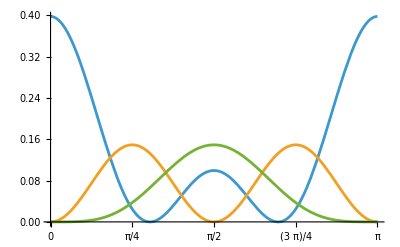

```mathematica
Plot[{ylmSquared[2,0,θ],ylmSquared[2,1,θ],ylmSquared[2,2,θ]},{θ,0,Pi},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

### The Exact Solutions — Radial Wave Functions

```mathematica
R[n_,l_,r_]:= 2/n^2 √(Factorial[n-1-l]/Factorial[n+l]^3) ((2 r)/n)^l Exp[-r/n] Factorial[n+l] LaguerreL[n-l-1,2 l+1,2r/n];
```

We’ll be squaring these too, so it might be handy to define:

```mathematica
rnlSquared[n_,l_,r_]:=Abs[R[n,l,r]]^2
```

```mathematica
Plot[{rnlSquared[3,0,r],rnlSquared[3,1,r],rnlSquared[3,2,r]},{r,0,20},Ticks->{Range[0,10,1],0,1},PlotRange->{{0,20},{0,0.01}}]
```

Let’s look at a few with n=3, and l=0, 1, and 2.

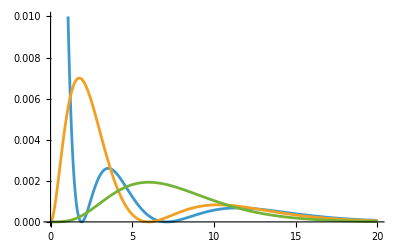

### Allowed Quantum Numbers and Total Energy

Not all combinations of quantum numbers are allowed. The only ones that correspond to solutions must be in these these ranges:

n=1,2,3,4, etc.
l=0,1,2,...,n-1
m=-l,-l+1, ..., -1, 0,1, ..., l-1,l 

The energy is entirely determined by the value of n and if you choose all the units conveniently the energy is just -1/n^2.

You might be wondering what a minus sign is doing in the energy. It is there because the Coulomb potential is attractive and it gets more and more negative as you the electron gets closer to the nucleus. So there is positive kinetic energy and negative potential energy. If you have an electron with total positive energy (kinetic plus potential), it flies away from the Hydrogen atom (leaving the proton sitting alone, as a positive ion).

### Normalization

The messy formulas above were messy in part because these solutions are already normalized.

### Time-Dependence